# Vectors and matrices with Mathematica

## Vectors

#### Write vectors componentwise in curly braces, separated by commas

```mathematica
a = {1,2,3}
```

{1,2,3}

```mathematica
b = {-1,0,2}
```

{-1,0,2}

#### Vector operations

Addition / subtraction

```mathematica
a + b
```

{0,2,5}

```mathematica
a-b
```

{2,2,1}

Multiplication by scalars

```mathematica
2a
```

{2,4,6}

```mathematica
2 a+ 3b
```

{-1,4,12}

#### Dot product

Use period, or Dot function

```mathematica
a.b
```

5

```mathematica
Dot[a,b]
```

5

#### Elementwise multiplication

Ordinary multiplication notation does elementwise product

```mathematica
a b
```

{-1,0,6}

Be careful not to do this when you mean to compute a dot product!

#### Cross product

The Cross function does cross products

```mathematica
Cross[a,b]
```

{4,-5,2}

#### Vectors can be defined symbolically

```mathematica
p = {x, y}
```

{x,y}

```mathematica
q = {s, t}
```

{s,t}

```mathematica
p.q
```

s x+t y

```mathematica
p q
```

{s x,t y}

```mathematica
h
```

h

```mathematica
p+q
```

{s+x,t+y}

### A handy function for visualization

```mathematica
showVecs[v1_, v2_,label_:""]:=
Graphics[
{
{Red,Arrow[{{0,0},v1}]},
{Blue, Arrow[{{0,0},v2}]}
},
PlotRange->{{-2,2},{-2,2}},
Frame->True,
FrameStyle->Medium,
GridLines->Automatic,
FrameLabel->{"x","y",label,None}
]
```

```mathematica
iHat={1,0}; jHat = {0,1}
```

{0,1}

```mathematica
Subscript[A, 0]={{2,-1},{-1,2}}
```

(2 | -1
-1 | 2)

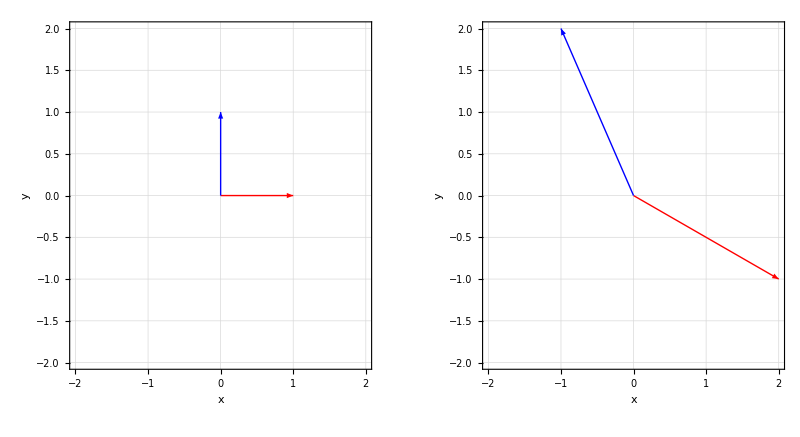

```mathematica
GraphicsRow[{showVecs[iHat,jHat,IdentityMatrix[2]],showVecs[Subscript[A, 0].iHat,Subscript[A, 0].jHat,Subscript[A, 0]]}]
```

## Matrices

### Forming matrices

Use curly braces

```mathematica
B = {{1,2},{3,4},{5,6}}
```

(1 | 2
3 | 4
5 | 6)

```mathematica
Transpose[B]
```

(1 | 3 | 5
2 | 4 | 6)

### Matrix-vector multiplication

Use the dot operator

```mathematica
{{1,2},{3,4},{5,6}}.{x,y}//MatrixForm
```

(x+2 y
3 x+4 y
5 x+6 y)

No dot --> elementwise (identical to “dot-star” in matlab)

```mathematica
{{1,2},{3,4},{5,6}}{x,y, z}//MatrixForm
```

(x | 2 x
3 y | 4 y
5 z | 6 z)

### Some special matrices

#### Anisotropic scaling

```mathematica
Remove[A]
```

```mathematica
Subscript[A, sc][s_]={{s,0},{0,1}}
```

(s | 0
0 | 1)

```mathematica
Manipulate[GraphicsRow[{showVecs[iHat,jHat,IdentityMatrix[2]],
showVecs[Subscript[A, sc][s].iHat,Subscript[A, sc][s].jHat,Subscript[A, sc][s]]}],{{s,1},-2,2,0.1}]
```

#### Shear

```mathematica
Subscript[A, sh][s_]={{1,s},{0,1}}
```

(1 | s
0 | 1)

```mathematica
Manipulate[GraphicsRow[{showVecs[iHat,jHat,IdentityMatrix[2]],showVecs[Subscript[A, sh][s].iHat,Subscript[A, sh][s].jHat,Subscript[A, sh][s]]}],
{{s,0},-2,2,0.1}]
```

#### Plane rotation

```mathematica
R[θ_]={{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}
```

(cos(θ) | -sin(θ)
sin(θ) | cos(θ))

```mathematica
Manipulate[GraphicsRow[{showVecs[iHat,jHat, IdentityMatrix[2]],showVecs[R[θ].iHat,R[θ].jHat,R[θ]]}],{{θ,0},-Pi,Pi,0.1}]
```

#### Reflection

### Composition

```mathematica
Manipulate[GraphicsRow[{
showVecs[iHat,jHat, IdentityMatrix[2]],
showVecs[R[θ].iHat,R[θ].jHat,R[θ]],
showVecs[Subscript[A, sh][s].(R[θ].iHat), Subscript[A, sh][s].(R[θ].jHat), "A.(R.x)"]}],{{θ,0},-Pi,Pi,0.1},
{{s,0},-2,2}]
```

```mathematica
Manipulate[GraphicsRow[{
showVecs[iHat,jHat, IdentityMatrix[2]],
showVecs[Subscript[A, sh][s].iHat,Subscript[A, sh][s].jHat,Subscript[A, sh][s]], 
showVecs[R[θ].(Subscript[A, sh][s].iHat), R[θ].(Subscript[A, sh][s].jHat), "R.(A.x)"]}],{{θ,0},-Pi,Pi,0.1},
{{s,0},-2,2}]
```

### Matrix-matrix multiplication

```mathematica
AA={{1,2},{3,4},{5,6}}
```

(1 | 2
3 | 4
5 | 6)

```mathematica
BB={{10,20},{30,40}}
```

(10 | 20
30 | 40)

You can multiply a 3×2 times a 2×2 matrix

```mathematica
AA.BB
```

(70 | 100
150 | 220
230 | 340)

A 2×2 can’t be multiplied into a 3×2 matrix.

```mathematica
BB.AA
```

Dot::dotsh: Tensors (10 | 20
30 | 40) and (1 | 2
3 | 4
5 | 6) have incompatible shapes.

(10 | 20
30 | 40).(1 | 2
3 | 4
5 | 6)

```mathematica
ShearThenRotate[s_,θ_]=R[θ].Subscript[A, sh][s]
```

(cos(θ) | s cos(θ)-sin(θ)
sin(θ) | cos(θ)+s sin(θ))

```mathematica
RotateThenShear[s_,θ_]=Subscript[A, sh][s].R[θ]
```

(cos(θ)+s sin(θ) | s cos(θ)-sin(θ)
sin(θ) | cos(θ))

### Solving linear systems

Solving A x = b

#### The LinearSolve function

```mathematica
AA = {{1,2},{2,3}}
```

(1 | 2
2 | 3)

```mathematica
b = {4,5}
```

{4,5}

Warning: Mathematica makes no distinction between row vectors and column vectors

Solve AA.x = b; expect solution {-2,3}

```mathematica
LinearSolve[AA,b]
```

{-2,3}

Solution is as expected

```mathematica
Solve[{Subscript[x, 1]+2 Subscript[x, 2]==4,2 Subscript[x, 1]+3 Subscript[x, 2]==5},{Subscript[x, 1],Subscript[x, 2]}]
```

{{x_1→-2,x_2→3}}

Another example:

```mathematica
AA = Table[i j /(1 + i + j),{i,1,5},{j,1,5}]
```

(1/3 | 1/2 | 3/5 | 2/3 | 5/7
1/2 | 4/5 | 1 | 8/7 | 5/4
3/5 | 1 | 9/7 | 3/2 | 5/3
2/3 | 8/7 | 3/2 | 16/9 | 2
5/7 | 5/4 | 5/3 | 2 | 25/11)

```mathematica
b = Table[i^2, {i, 1, 5}]
```

{1,4,9,16,25}

```mathematica
LinearSolve[AA,b]
```

{3465,-17920,39060,-37800,13398}

```mathematica
AA={{E, Pi, Sqrt[2]}, {1, 2, 3}, {(Sqrt[5]-1)/2, Sqrt[Pi], E^2}}
```

(ⅇ | π | √2
1 | 2 | 3
1/2 (√5-1) | √π | ⅇ^2)

```mathematica
b = {Pi/2, Sqrt[E], 4}
```

{π/2,√ⅇ,4}

```mathematica
LinearSolve[AA,b]
```

{(-16 √2+24 π+2 ⅇ^2 π-2 ⅇ^(5/2) π-3 π^(3/2)+2 √(2 ⅇ π))/(2 √2-2 √10+4 ⅇ^3-6 ⅇ √π-3 π+3 √5 π-2 ⅇ^2 π+2 √(2 π)),-(16 √2-48 ⅇ+4 ⅇ^(7/2)+2 √(2 ⅇ)-2 √(10 ⅇ)-3 π+3 √5 π-2 ⅇ^2 π)/(2 (-2 √2+2 √10-4 ⅇ^3+6 ⅇ √π+3 π-3 √5 π+2 ⅇ^2 π-2 √(2 π))),(-16 ⅇ+2 ⅇ^(3/2) √π+7 π+√5 π+√ⅇ π-√(5 ⅇ) π-π^(3/2))/(-2 √2+2 √10-4 ⅇ^3+6 ⅇ √π+3 π-3 √5 π+2 ⅇ^2 π-2 √(2 π))}

```mathematica
LinearSolve[AA,N[b]]
```

{0.782066,-0.438253,0.581054}

```mathematica
Remove[p,q,r,s]
```

```mathematica
LinearSolve[{{p,q},{r,s}},{v,w}]
```

{(s v-q w)/(p s-q r),(r v-p w)/(q r-p s)}

```mathematica
h
```

h

#### Inverse matrices

```mathematica
AInv = Inverse[AA]
```

((2 ⅇ^2-3 √π)/(√2-√10+2 ⅇ^3-3 ⅇ √π-(3 π)/2+(3 √5 π)/2-ⅇ^2 π+√(2 π)) | (√(2 π)-ⅇ^2 π)/(√2-√10+2 ⅇ^3-3 ⅇ √π-(3 π)/2+(3 √5 π)/2-ⅇ^2 π+√(2 π)) | (3 π-2 √2)/(√2-√10+2 ⅇ^3-3 ⅇ √π-(3 π)/2+(3 √5 π)/2-ⅇ^2 π+√(2 π))
(-3/2+(3 √5)/2-ⅇ^2)/(√2-√10+2 ⅇ^3-3 ⅇ √π-(3 π)/2+(3 √5 π)/2-ⅇ^2 π+√(2 π)) | (1/(√2)-√(5/2)+ⅇ^3)/(√2-√10+2 ⅇ^3-3 ⅇ √π-(3 π)/2+(3 √5 π)/2-ⅇ^2 π+√(2 π)) | (√2-3 ⅇ)/(√2-√10+2 ⅇ^3-3 ⅇ √π-(3 π)/2+(3 √5 π)/2-ⅇ^2 π+√(2 π))
(1-√5+√π)/(√2-√10+2 ⅇ^3-3 ⅇ √π-(3 π)/2+(3 √5 π)/2-ⅇ^2 π+√(2 π)) | (-ⅇ √π-π/2+(√5 π)/2)/(√2-√10+2 ⅇ^3-3 ⅇ √π-(3 π)/2+(3 √5 π)/2-ⅇ^2 π+√(2 π)) | (2 ⅇ-π)/(√2-√10+2 ⅇ^3-3 ⅇ √π-(3 π)/2+(3 √5 π)/2-ⅇ^2 π+√(2 π)))

Solve A x=b for x by computing x = A^-1 b. Analogous to solving 3x=2 by computing x=3^-1 2

```mathematica
AInv . b
```

{((2 ⅇ^2-3 √π) π)/(2 (√2-√10+2 ⅇ^3-3 ⅇ √π-(3 π)/2+(3 √5 π)/2-ⅇ^2 π+√(2 π)))+(4 (3 π-2 √2))/(√2-√10+2 ⅇ^3-3 ⅇ √π-(3 π)/2+(3 √5 π)/2-ⅇ^2 π+√(2 π))+(√ⅇ (√(2 π)-ⅇ^2 π))/(√2-√10+2 ⅇ^3-3 ⅇ √π-(3 π)/2+(3 √5 π)/2-ⅇ^2 π+√(2 π)),(4 (√2-3 ⅇ))/(√2-√10+2 ⅇ^3-3 ⅇ √π-(3 π)/2+(3 √5 π)/2-ⅇ^2 π+√(2 π))+(√ⅇ (1/(√2)-√(5/2)+ⅇ^3))/(√2-√10+2 ⅇ^3-3 ⅇ √π-(3 π)/2+(3 √5 π)/2-ⅇ^2 π+√(2 π))+((-3/2+(3 √5)/2-ⅇ^2) π)/(2 (√2-√10+2 ⅇ^3-3 ⅇ √π-(3 π)/2+(3 √5 π)/2-ⅇ^2 π+√(2 π))),(4 (2 ⅇ-π))/(√2-√10+2 ⅇ^3-3 ⅇ √π-(3 π)/2+(3 √5 π)/2-ⅇ^2 π+√(2 π))+((1-√5+√π) π)/(2 (√2-√10+2 ⅇ^3-3 ⅇ √π-(3 π)/2+(3 √5 π)/2-ⅇ^2 π+√(2 π)))+(√ⅇ (-ⅇ √π-π/2+(√5 π)/2))/(√2-√10+2 ⅇ^3-3 ⅇ √π-(3 π)/2+(3 √5 π)/2-ⅇ^2 π+√(2 π))}

### Determinants